### Effect of larger rule space on adaptive precision

#### Import

CloudObject[https://www.wolframcloud.com/obj/willemnielsen1/progrus]

CloudObject[https://www.wolframcloud.com/obj/willemnielsen1/progrus2]

#### Code

```mathematica
Module[
{goal=50,deep=6000,cut=200,ru,life,evo,data},
Column[ParallelTable[Row[
SeedRandom[745746+i];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#],5],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life!=-Infinity&&Abs[life-goal
]<=Abs[Last[#]-goal],{ru,life},#]
]&,{{0,3,1},1},deep];
evo=First/@SplitBy[evo,Last];
Map[CompoundExpression[
data=CellularAutomaton[
First[#],{{1},0},Last[#]+2],
Labeled[ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
ImageSize->{Automatic,15Sqrt[Length[data]+1]}
],Style[Last[#],"Text",Italic,Gray,11]]
]&,evo]],{i,{1,5,16,51,54}}],
Dividers->{False,Thread[Range[2,5]->LightGray]}
]

]
```

```mathematica
progrus = Module[
{goal=30,deep=5000,cut=60,ru,life,evo,data},
Table[
ParallelTable[
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#],5],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life!=-Infinity&&Abs[life-goal
]<=Abs[Last[#]-goal],{ru,life},#]
]&,{{0,i,1},1},deep], {j, 5}], {i, 3, 10}]];
```

```mathematica
progrus2 = Module[
{goal=30,deep=5000,cut=60,ru,life,evo,data},
Table[
ParallelTable[
SeedRandom[324564+ i + j];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#],5],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life!=-Infinity&&Abs[life-goal
]<=Abs[Last[#]-goal],{ru,life},#]
]&,{{0,i,1},1},deep], {j, 5}], {i, 3, 10}]];
```

#### Effect of larger rule space on adaptive precision (relevant for bigger brains)

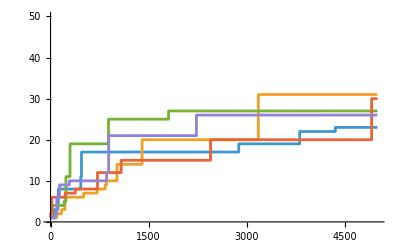
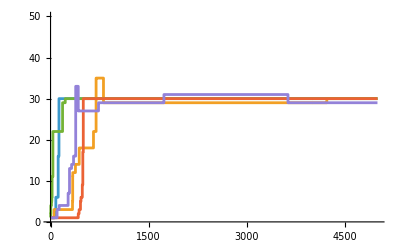
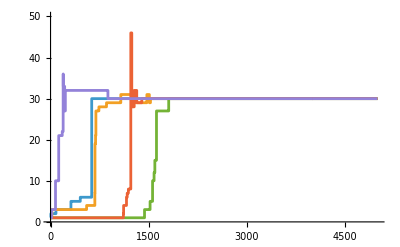
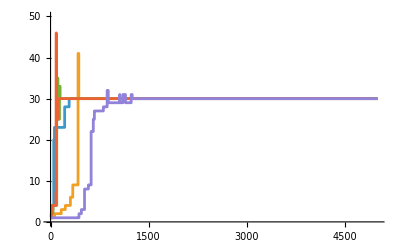
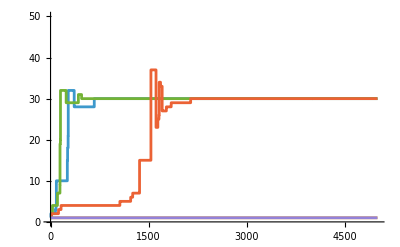
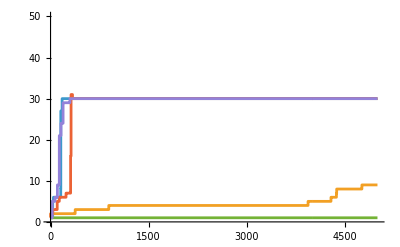
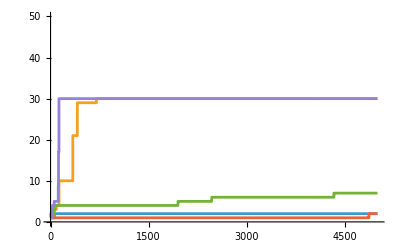
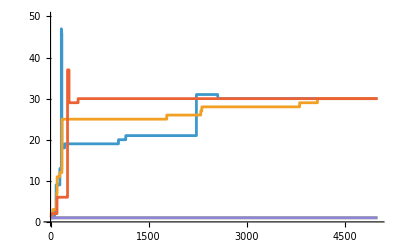
{-Graphics-k = 3 , r = 1,-Graphics-k = 4 , r = 1,-Graphics-k = 5 , r = 1,-Graphics-k = 6 , r = 1,-Graphics-k = 7 , r = 1,-Graphics-k = 8 , r = 1,-Graphics-k = 9 , r = 1,-Graphics-k = 10 , r = 1}

```mathematica
MapThread[Labeled[ListStepPlot[#1, PlotHighlighting->None, PlotRange->{Automatic, {0, 50}}], Text["k = "<>ToString[#2]", r = 1"]]&, {progrus2[[All, All, All, -1]], Range[3, 10]}]
```

```mathematica
CloudConnect["willemnielsen1@gmail.com"]
```

willemnielsen1@gmail.com

```mathematica
$CloudUserID
```

willemnielsen1@gmail.com